Henry Osei

Experiment 9.1

```mathematica
concaveTest[f_,a_,b_]:=DynamicModule[{x,g,p1,p2},g[x_]=f[x];Manipulate[p1=Plot[g[x],{x,a,b},PlotStyle->RGBColor[0,0,1]];
    p2=Plot[g[x1]+((g[x1+d]-g[x1])/(d))*(x-x1),{x,x1,x1+d},PlotStyle->RGBColor[1,0,0]];Show[p1,p2],{x1,a,b},{{d,(b-a)/3,"Width"},0,b-x1}]]
```

```mathematica
concaveTest[f_,a_,b_]:=DynamicModule[{x,g,p1,p2},g[x_]=f[x];Manipulate[p1=Plot[g[x],{x,a,b},PlotStyle->RGBColor[0,0,1]];
    p2=Plot[g[x1]+((g[x1+d]-g[x1])/(d))*(x-x1),{x,x1,x1+d},PlotStyle->RGBColor[1,0,0]];Show[p1,p2],{x1,a,b},{{d,(b-a)/3,"Width"},0,b-x1}]]
Clear[f,x];
f[x_]:=Exp[-x^2];
concaveTest[f,-3,3]
```

```mathematica
Yes, f1 is concave donw on (-1/Sqrt2,1/sqrt2. It is not concave up on (-3,-1/sqrt2,1/sqrt2,3)
```

```mathematica
concaveTest[f_,a_,b_]:=DynamicModule[{x,g,p1,p2},g[x_]=f[x];Manipulate[p1=Plot[g[x],{x,a,b},PlotStyle->RGBColor[0,0,1]];
    p2=Plot[g[x1]+((g[x1+d]-g[x1])/(d))*(x-x1),{x,x1,x1+d},PlotStyle->RGBColor[1,0,0]];Show[p1,p2],{x1,a,b},{{d,(b-a)/3,"Width"},0,b-x1}]]
Clear[f,x];
f[x_]:=x^3-4x+1;
concaveTest[f,-2,2]
```

```mathematica
X=-1,0 and 1 are all POI because these points are points where concavity changes.
```

```mathematica
concaveTest[f_,a_,b_]:=DynamicModule[{x,g,p1,p2},g[x_]=f[x];Manipulate[p1=Plot[g[x],{x,a,b},PlotStyle->RGBColor[0,0,1]];
    p2=Plot[g[x1]+((g[x1+d]-g[x1])/(d))*(x-x1),{x,x1,x1+d},PlotStyle->RGBColor[1,0,0]];Show[p1,p2],{x1,a,b},{{d,(b-a)/3,"Width"},0,b-x1}]]
Clear[f,x];
f[x_]:=Log[x-1/(3x-6)];
concaveTest[f,0,2]
```

```mathematica
LinguisticAssistant
```

Exp 9.2

```mathematica
slopeTest[f_,a_,b_]:=DynamicModule[{x,g,p1,p2},g[x_]=f[x];Manipulate[p1=Plot[g[x],{x,a,b},PlotStyle->RGBColor[0,0,1]];
                 p2=Plot[g[x0]+g'[x0](x-x0),{x,a,b},PlotStyle->RGBColor[1,0,0]];
Show[p1,p2],{{x0,(a+b)/2},a,b}]]
Clear f[x_];
f[x_]:=Exp[-x^2];
slopeTest[f,-3,3]
```

```mathematica
F1 is concave downward (-3,3)
```

```mathematica
slopeTest[f_,a_,b_]:=DynamicModule[{x,g,p1,p2},g[x_]=f[x];Manipulate[p1=Plot[g[x],{x,a,b},PlotStyle->RGBColor[0,0,1]];
                 p2=Plot[g[x0]+g'[x0](x-x0),{x,a,b},PlotStyle->RGBColor[1,0,0]];
Show[p1,p2],{{x0,(a+b)/2},a,b}]]
Clear f[x_];
f[x_]:=x^3-4x+1;
slopeTest[f,-2,2]
```

```mathematica
There are POI at x=-1,0,1 because concavity changes on these points.
```

```mathematica
slopeTest[f_,a_,b_]:=DynamicModule[{x,g,p1,p2},g[x_]=f[x];Manipulate[p1=Plot[g[x],{x,a,b},PlotStyle->RGBColor[0,0,1]];
                 p2=Plot[g[x0]+g'[x0](x-x0),{x,a,b},PlotStyle->RGBColor[1,0,0]];
Show[p1,p2],{{x0,(a+b)/2},a,b}]]
Clear f[x_];
f[x_]:=Log[x-1/(3x-6)];
slopeTest[f,0,2]
```

```mathematica
f3 is concave down at (0,1). Concave up at (1.5,2)
```

Exp 9.3

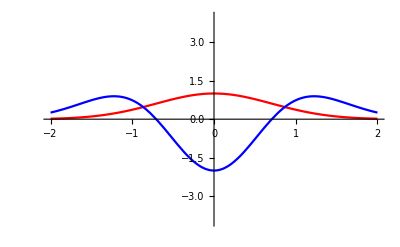

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-√(1/2 (1-2 ProductLog[-(3 √ⅇ)/4]))},{x→√(1/2 (1-2 ProductLog[-(3 √ⅇ)/4]))}}

```mathematica
Clear[f];
f[x_]:=Exp[-x^2];
Plot[{f[x],f''[x]},{x,-2,2},PlotRange->{-4,4},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
Solve[f''[x]==3,x]
```

```mathematica
F1 is indeed concave downward on (Yes, f1 is concave downward on (-1/Sqrt2,1/sqrt2. (-3,-1/sqrt2,1/sqrt2,3)
```

```mathematica
Clear[f];
f[x_]:=x^3-4x+1;
Plot[{f[x],f''[x]},{x,-2,2},PlotRange->{-4,4},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
Solve[f''[x]==-1,x]
```

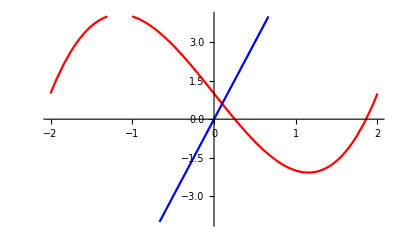

```mathematica
{{x->-1/6}}
There are indeed POI on x= -1,0,1. These points are where concavity changes.
```

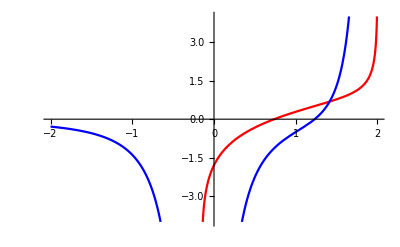

{{x→2+1/(6 √(3/(-24+(23112-1296 √318)^(1/3)+6 (107+6 √318)^(1/3))))-1/2 √(-16/9-1/27 (23112-1296 √318)^(1/3)-2/9 (107+6 √318)^(1/3)-8 √(3/(-24+(23112-1296 √318)^(1/3)+6 (107+6 √318)^(1/3))))},{x→2+1/(6 √(3/(-24+(23112-1296 √318)^(1/3)+6 (107+6 √318)^(1/3))))+1/2 √(-16/9-1/27 (23112-1296 √318)^(1/3)-2/9 (107+6 √318)^(1/3)-8 √(3/(-24+(23112-1296 √318)^(1/3)+6 (107+6 √318)^(1/3))))},{x→2-1/(6 √(3/(-24+(23112-1296 √318)^(1/3)+6 (107+6 √318)^(1/3))))-1/2 √(-16/9-1/27 (23112-1296 √318)^(1/3)-2/9 (107+6 √318)^(1/3)+8 √(3/(-24+(23112-1296 √318)^(1/3)+6 (107+6 √318)^(1/3))))},{x→2-1/(6 √(3/(-24+(23112-1296 √318)^(1/3)+6 (107+6 √318)^(1/3))))+1/2 √(-16/9-1/27 (23112-1296 √318)^(1/3)-2/9 (107+6 √318)^(1/3)+8 √(3/(-24+(23112-1296 √318)^(1/3)+6 (107+6 √318)^(1/3))))}}

```mathematica
Clear[f];
f[x_]:=Log[x-1/(3x-6)];
Plot[{f[x],f''[x]},{x,-2,2},PlotRange->{-4,4},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
Solve[f''[x]==0,x]
```